# Práctica (11-10-2017) Números complejos.

Expresar un número compejo de diferentes formas y calcular sumas, productos, inversos, cocientes, módulos, argumetnos, raíces, potencias, exponenciales, logaritmos, senos y cosenos.

```mathematica
2+ 3 I
```

2+3 ⅈ

```mathematica
(2 + 3I) + (5 - 4 I)
```

7-ⅈ

```mathematica
(2 + 3 I) * (55 - 123 I)
```

479-81 ⅈ

```mathematica
(2 * 3 I)^-1
```

-ⅈ/6

```mathematica
(5 - 4i) ^-1
```

1/(5-4 i)

```mathematica
(5 - 4 I) ^-1
```

5/41+(4 ⅈ)/41

```mathematica
(2 + 3I) / (54 + 23 I)
```

177/3445+(116 ⅈ)/3445

```mathematica
Abs[(5 - 4I)]
```

√41

```mathematica
Abs [(55555555 - 444444444 I)]
```

√200617283493827161

```mathematica
Arg[(5 - 4I)]
```

-ArcTan[4/5]

```mathematica
N[Out[10]]
```

-0.674741

```mathematica
Cos[30Degree]
```

(√3)/2

```mathematica
N[Out[12]]
```

0.866025

```mathematica
N[Out[12] Degree]
```

0.015115

```mathematica
(5 - 4i) ^37
```

(5-4 i)^37

```mathematica
Sqrt(41) ^37
```

470980252977060692221811837930860485365142108678565170347081 Sqrt

```mathematica
Sqrt [41] ^37
```

107178930967531784356353269521 √41

```mathematica
N[Out[19]]
```

6.8628×10^29

```mathematica
Sqrt[-1]
```

ⅈ

```mathematica
Sqrt[-1]^ 1/7
```

ⅈ/7

```mathematica
Abs[-1 + 0I]
```

1

```mathematica
Arg[-1]
```

π

```mathematica
-1^(1/7)
```

(-1)^(1/7)

```mathematica
ComplexExpand[Out[25]]
```

Cos[π/7]+ⅈ Sin[π/7]

```mathematica
ComplexExpand[Solve[z^7 == -1,z]]
```

{{z→-1},{z→Cos[π/7]+ⅈ Sin[π/7]},{z→-ⅈ Cos[(3 π)/14]-Sin[(3 π)/14]},{z→ⅈ Cos[π/14]+Sin[π/14]},{z→-ⅈ Cos[π/14]+Sin[π/14]},{z→ⅈ Cos[(3 π)/14]-Sin[(3 π)/14]},{z→Cos[π/7]-ⅈ Sin[π/7]}}

```mathematica
raices = Table[1 (Cos[Pi/7 + k 2Pi/7] + I Sin [Pi/7 + k 2 Pi/7]), {k, 0, 6}]
```

{Cos[π/7]+ⅈ Sin[π/7],ⅈ Cos[π/14]+Sin[π/14],ⅈ Cos[(3 π)/14]-Sin[(3 π)/14],-1,-ⅈ Cos[(3 π)/14]-Sin[(3 π)/14],-ⅈ Cos[π/14]+Sin[π/14],Cos[π/7]-ⅈ Sin[π/7]}

```mathematica
Puntos = Table[{Re[raices[[i]]], Im[raices[[i]]]}, {i, 1, 7}]
```

{{Cos[π/7],Sin[π/7]},{Sin[π/14],Cos[π/14]},{-Sin[(3 π)/14],Cos[(3 π)/14]},{-1,0},{-Sin[(3 π)/14],-Cos[(3 π)/14]},{Sin[π/14],-Cos[π/14]},{Cos[π/7],-Sin[π/7]}}

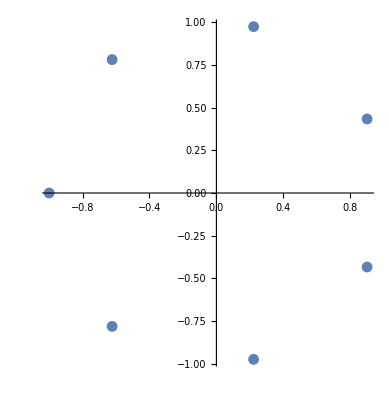

```mathematica
p = ListPlot[Puntos, AspectRatio-> Automatic]
```



```mathematica
c = ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2 Pi}]
```

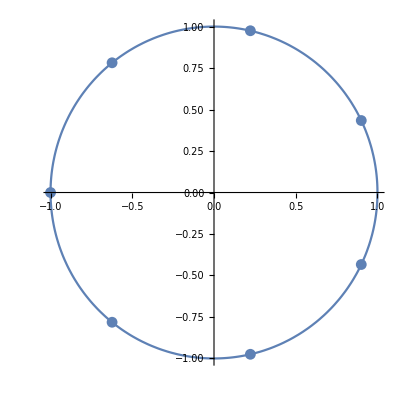

```mathematica
Show[p, c, PlotRange -> All]
```